```mathematica
SetDirectory["/home/stnav/Projects/jensen-lab-analysis"]
```

/home/stnav/Projects/jensen-lab-analysis

-Graphics-

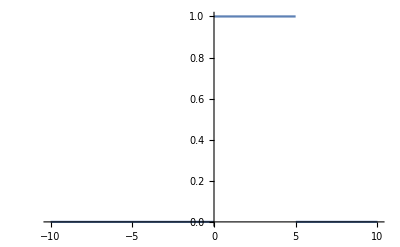

```mathematica
target = ExampleData[{"TestImage", "ResolutionChart"}]//ImageResize[#, {160, 160}]&// ImageData//(1-#)& //Image
```

```mathematica
λ=791/125000;
source[y_]:=UnitBox[y];
kernel[y_,t_]:=Exp[-I π/4]Exp[I π y^2/(λ t)]/√(λ t);u[x_,t_]=Piecewise[{{Convolve[source[y],kernel[y,t],y,x,Assumptions->t>0],t>0}},source[x]];
```

```mathematica
Manipulate[
Plot[Abs[u[x,v/λ]]^2,{x,-1,1},PlotRange->{{-1,1},{0,1.8}},Filling->Axis,ImageSize->{500,350}],
{{v,0,"distance from slit"},0,1,Appearance->"Labeled"},SaveDefinitions->True,TrackedSymbols->True]
```

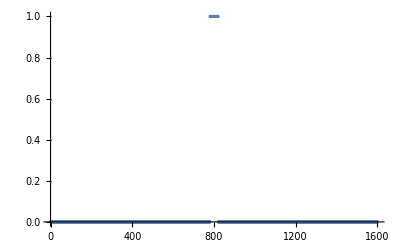

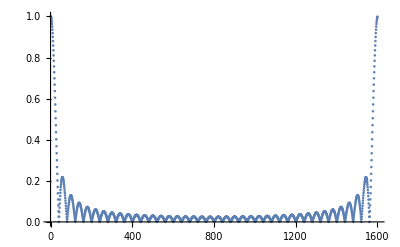

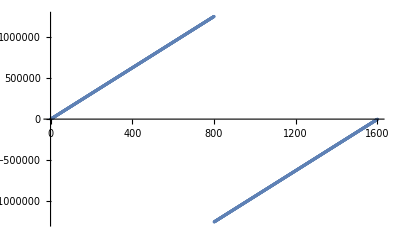

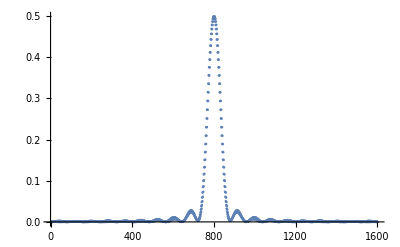

```mathematica
λ=660*10^-9(*nm*);{xmin,xmax}={-2,2}*10^-3(*mm*);a=0.1*10^-3(*mm*);z=3*10^-2(*cm*);n=1600;
k=2 π/λ//N;d=(xmax-xmin)/(n-1);
target=Table[UnitStep[x+a/2]-UnitStep[x-a/2],{x,xmin,xmax,d}];
kx=Join[Range[0,n/2-1],Range[-n/2,-1]]/(d*n)*2 π//N;
H=Exp[I*z*Sqrt[k^2-kx^2]];
A=target;
Ak=Fourier[A];
Az=InverseFourier[Ak*H];

ListPlot[A, PlotRange->All]
ListPlot[Abs[Ak],PlotRange->All]
ListPlot[kx, PlotRange->All]
ListPlot[Abs[Az]^2,PlotRange->All]
```

```mathematica
Length[Ak]
Length[kx]
```

1600

1600

```mathematica
λ=660*10^-9(*nm*);{xmin,xmax}={-2,2}*10^-3(*mm*);a=0.1*10^-3(*mm*);z=3*10^-2(*cm*);n=1600;
k=2 π/λ//N;d=(xmax-xmin)/(n-1);
target=Table[UnitStep[x+a/2]-UnitStep[x-a/2],{x,xmin,xmax,d}];
ListPlot[target]
kx=Join[Range[0,n/2-1],Range[-n/2,-1]]/(d*n)*2 π//N;
H=Exp[ⅈ*z*Sqrt[k^2-kx^2]];
A=target;
Ak=Fourier[A];
Az=InverseFourier[Ak*H];
```

-Graphics-

```mathematica
ClearAll["Global`*"]

(*λ=660*10^-9(*nm*);{xmin,xmax}={-2,2}*10^-3(*mm*);a=0.1*10^-3(*mm*);z=3*10^-2(*cm*);n=1600;*)
k=2 π/λ;
d=(xmax-xmin)/(n-1);

target[x_]:=UnitStep[x+a/2]-UnitStep[x-a/2]
A[x_]= target[x]
Ak[kx_]=FourierTransform[A[x], x, kx]
H[z_,kx_]=Exp[ⅈ*z*Sqrt[k^2-kx^2]]
Ak[kx]*H[z, kx]
InverseFourierTransform[Ak[kx]*H[0, kx],kx, x]//FullSimplify
```

-UnitStep[-a/2+x]+UnitStep[a/2+x]

```mathematica
(√(2/π) Sin[(a kx)/2])/kx
```

ⅇ^(ⅈ z √(-kx^2+(4 π^2)/λ^2))

(ⅇ^(ⅈ z √(-kx^2+(4 π^2)/λ^2)) √(2/π) Sin[(a kx)/2])/kx

1/2 (Sign[a-2 x]+Sign[a/2+x])